```mathematica
test=makeTrack[500,1,10,{10,1/10,π},5];
```

```mathematica
Count[test[[2]],{_,_,_}]
```

100

```mathematica
Position[test[[1]],{_,_}]
```

{{8},{18},{28},{38}}

```mathematica
Position[test[[1]],{{_,_,_}}]
```

{{13},{23},{33}}

## Fundamental diagram

A fundamental diagram is a plot of density versus flow. This is a measurement of what is the amount of vehicles that pass through a given section of the road as a function of the number of vehicles on the whole road. I find that flow is a little hard to measure (since busses don’t have an ID, they are hard to count only once).  
Therefore, I propose to do a plot of average speed vs. density.
To reproduce this, define a track size, set a density ρ, define lights and stops, run a simulation for T=1000 size and (after a transient = 1000) just add up all speeds and divide over the number of buses for each tick, then average over all ticks.

```mathematica
$HistoryLength=0;
```

No stations, no lights

```mathematica
For[
fundamental={};ρb=.1,ρb≤1,ρb=ρb+1/10,
tr=makeTrack[1000,ρb,2000,{2000,1/10,π},5000];
sim=busSimulation[tr,5000];
Print[ToString[ρb]<>" done."];
AppendTo[fundamental,{ρb,Mean[Mean/@(Cases[#[[2]],{v_,_,_}->v]&/@sim)]}];
]
```

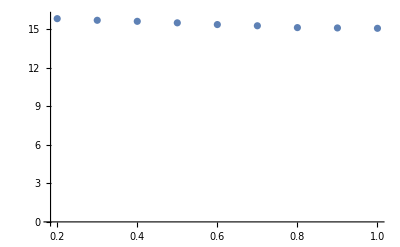

```mathematica
ListPlot[fundamental,PlotRange->{0,vmax}]
```

Stations every 200 ticks, no lights
	◦ An attempt of a track of size 5000 kills the machine

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jovillal/git/Bus-station-and-light-simulation

```mathematica
toFileName[p_Real]:="rho0"<>ToString[IntegerPart[10 p]]<>".txt";
toFileName[p_Integer]:="rho"<>ToString[IntegerPart[p]]<>".txt";
```

```mathematica
For[
fundamental={};ρb=.1,ρb≤1,ρb=ρb+1/10,
tr=makeTrack[4000,ρb,200,{20000,1/10,π},4000];
sim=busSimulation[tr,5000];
Export[toFileName[ρb],sim];
Print[ToString[ρb]<>" done."];
AppendTo[fundamental,{ρb,Mean[Mean/@(Cases[#[[2]],{v_,_,_}->v]&/@sim)]}];
]
```

0.1 done.

0.2 done.

0.3 done.

0.4 done.

0.5 done.

0.6 done.

0.7 done.

0.8 done.

0.9 done.

1. done.

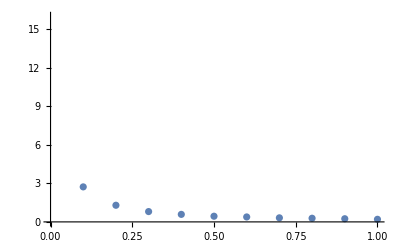

```mathematica
ListPlot[fundamental,PlotRange->{0,vmax}]
```

This is weird as shit... what is going on?

```mathematica
ρb=.2;
```

```mathematica
tr=makeTrack[5000,ρb,200,{20000,1/10,π},5000];
```

```mathematica
Count[tr[[1]],{___}]
```

25

```mathematica
tr[[2,1;;200]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,{100},{100},{100},{100},{7,0,100},{100},{100},{100},{100},{7,0,100},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,{100},{100},{100},{100},{7,0,100},0,0,0,0,0,0,0,{100},{100},{100},{100},{7,0,100},{100},{100},{100},{100},{7,0,100},{100},{100},{100},{100},{7,0,100},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,{100},{100},{100},{100},{7,0,100},{100},{100},{100},{100},{7,0,100},{100},{100},{100},{100},{7,0,100},{100},{100},{100},{100},{7,0,100},{100},{100},{100},{100},{7,0,100},{100},{100},{100},{100},{7,0,100},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,{100},{100},{100},{100},{7,0,100},0,0,0,0,0,0}

```mathematica
For[
fundamental={};ρb=.1,ρb≤1,ρb=ρb+1/10,
tr=makeTrack[5000,ρb,200,{20000,1/10,π},5000];
sim=busSimulation[tr,5000];
AppendTo[fundamental,{ρb,Count[Flatten[sim[[All,2]][[All,-(los+2w);;-1]],1],{_,_,_}]/Round[.8 Length[sim]]}];
]
```

## Move tests (don’t erase)

### track generating function

### movebottom

```mathematica
heads
```

{5,19,30,35,41,50,64,98,104,150,200,240,287,300,348,400,448,495,550,594,650,698,750,850,950,1050,1150,1250}

```mathematica
neighbors[[13,2]]
```

{{0},{0},{0},{0},{0,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
am
```

-7

```mathematica
Length[neighbors[[All,2]]]
```

21

```mathematica
16+am
```

9

```mathematica
b=13;
Column[{neighbors[[b,2]],
movebottom[neighbors[[b,2]]]}]
```

Bus ahead, moving

{{6,0,0},8}

Far, slow, hold or accelerate to max negative

Changing speed from 6 to 7

{{6,0,0},{},7}

{{0},{0},{0},{0},{6,0,0},0,0,0,0,0,0,0,0,{0},{0},{0},{0},{0,0,0},0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,{0},{0},{0},{0},{7,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
movebottom/@neighbors[[All,2]]
```

{{0,0,0,0,0,0,0,0,0,{0},{0},{0},{0},{9,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,{0},{0},{0},{0},{6,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{0},{0},{0},{0},{0,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,{0},{0},{0},{0},{1,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,{0},{0},{0},{0},{4,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{0},{0},{0},{0},{2,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{0},{0},{0},{0},{2,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,{0},{0},{0},{0},{1,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,{0},{0},{0},{0},{8,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,{0},{0},{0},{0},{9,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,{0},{0},{0},{0},{5,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,{0},{0},{0},{0},{16,0,0},0,0,0,0,0,0},{0,0,0,0,0,0,0,{0},{0},{0},{0},{7,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{0},{0},{0},{0},{2,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,{0},{0},{0},{0},{3,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,{0},{0},{0},{0},{7,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,{0},{0},{0},{0},{8,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,{0},{0},{0},{0},{16,0,0},0,0,0,0,0,0},{0,0,{100},{100},{100},{100},{2,{1,1},14},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,{0},{0},{0},{0},{6,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{100},{100},{100},{100},{2,{1,2},50},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,{0},{0},{0},{0},{4,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{100},{100},{100},{0},{2,{1,1},0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{0},{0},{0},{0},{2,{2,0},0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{100},{100},{100},{100},{2,{2,1},0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{100},{100},{100},{100},{2,{2,1},88},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{100},{100},{100},{100},{2,{2,415},0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,{100},{100},{100},{100},{6,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

### load/unload

```mathematica
Flatten[Position[heads,#]&/@{50, 150,  550, 650, 750, 850, 950, 1050, 1150,1250}]
```

{6,10,19,21,23,24,25,26,27,28}

```mathematica
Flatten[Position[heads,#]&/@{50, 150,  550, 650, 750, 850, 950, 1050, 1150,1250}]
```

{6,10,19,21,23,24,25,26,27,28}

```mathematica
move/@neighbors[[%]]
```

{{{0,0,0,0,{0,15},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{0},{0},{0},{0},{2,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{0,22},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{0},{0},{0},{0},{0,{2,0},0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{0,16},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{100},{100},{100},{99},{0,{2,399},0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{0,4},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{100},{100},{100},{100},{0,{1,1},35},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{0,11},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{100},{100},{85},{0},{0,{2,285},0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{0,9},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{0},{0},{0},{0},{0,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{0,3},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{100},{100},{100},{100},{0,{2,411},11},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{33,4},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{100},{100},{100},{100},{0,0,100},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{60,4},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{100},{100},{100},{100},{0,0,15},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{0,21},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{100},{100},{100},{100},{0,{1,8},0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
i=28;
Column[neighbors[[i]]]
move[neighbors[[i]]]
```

### lights

```mathematica
Flatten[Position[heads,#]&/@{200,300,400,495,594,698}]
```

{11,14,16,18,20,22}

```mathematica
move/@neighbors[[%]]
```

{{{0,0,0,0,{{15,0,0}},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{0},{0},{0},{0},{0,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{{15,0,0}},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{0},{0},{0},{0},{0,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,{{15,0,0}},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,{0},{0},{0},{0},{10,0,0},0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,{{15,1,0}},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,{0},{0},{0},{0},{16,0,0},0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,{{15,0,0}},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,{0},{0},{0},{0},{6,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,{{15,0,0}},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,{0},{0},{0},{0},{4,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
{11,14,16,18,20,22}
```

```mathematica
i=22;
Column[neighbors[[i]]]
move[neighbors[[i]]]
```

{0,0,0,0,0,0,{{15,0,0}},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{{0},{0},{0},{0},{2,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{0,0,0,0,0,0,{{15,0,0}},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,{0},{0},{0},{0},{2,0,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

### advanceOne

```mathematica
heads=Position[track[[2]],{_,_,_}]//Flatten;
neighbors={track[[1]][[#-w;;#+los]],track[[2]][[#-w;;#+los]]}&/@heads;
```

```mathematica
updated=advanceOne[track];
```

```mathematica
Length[heads]
```

30

```mathematica
bn=29;
neighbors[[bn]]//MatrixForm
move[neighbors[[bn]]]//MatrixForm
{updated[[1]][[#-w;;#+los]],updated[[2]][[#-w;;#+los]]}&[heads[[bn]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{0} | {0} | {0} | {0} | {14,0,1} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | {100} | {100} | {100} | {100})

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | {0} | {0} | {0} | {0} | {11,0,1} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | {0} | {0} | {0} | {0} | {11,0,1} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | {100} | {100} | {100} | {100})

```mathematica
track=updated;
```

### Simulation

```mathematica
data=busSimulation[100,100];
```

```mathematica
track=data[[10]];
```

For two steps back

```mathematica
old=track;
t=1;
updated=advanceOne[track];
```

```mathematica
old=updated;
t++;
updated=advanceOne[old];
```

WARNING!!! Had to brake too much.

WARNING: Braking more than allowed

```mathematica
t
```

18

```mathematica
heads=Position[updated[[2]],{_,_,_}]//Flatten;
neighbors={updated[[1]][[#-w;;#+los]],updated[[2]][[#-w;;#+los]]}&/@heads;
oldheads=Position[old[[2]],{_,_,_}]//Flatten;
oldneighbors={old[[1]][[#-w;;#+los]],old[[2]][[#-w;;#+los]]}&/@oldheads;
```

```mathematica
Length/@{oldheads,heads}
```

{30,30}

```mathematica
bn=1;
oldneighbors[[bn]]//MatrixForm
move[oldneighbors[[bn]]]//MatrixForm
neighbors[[bn]]//MatrixForm
(*{updated[[1]][[#-w;;#+vmax-am-1]],updated[[2]][[#-w;;#+vmax-am-1]]}&[heads[[bn]]]//MatrixForm*)
```

For three steps back

```mathematica
old=older=track;
t=1;
updated=advanceOne[track];
old=updated;
t++;
updated=advanceOne[old];
```

```mathematica
t++;
older=old;
old=updated;
updated=advanceOne[old];
```

WARNING: Braking more than allowed

```mathematica
t
```

41

```mathematica
heads=Position[updated[[2]],{_,_,_}]//Flatten;
neighbors={updated[[1]][[#-w;;#+los]],updated[[2]][[#-w;;#+los]]}&/@heads;
oldheads=Position[old[[2]],{_,_,_}]//Flatten;
oldneighbors={old[[1]][[#-w;;#+los]],old[[2]][[#-w;;#+los]]}&/@oldheads;
olderheads=Position[older[[2]],{_,_,_}]//Flatten;
olderneighbors={older[[1]][[#-w;;#+los]],older[[2]][[#-w;;#+los]]}&/@olderheads;
```

```mathematica
Length/@{olderheads,oldheads,heads}
```

{30,30,30}

```mathematica
bn=25;
olderneighbors[[bn]]//MatrixForm
move[olderneighbors[[bn]]]//MatrixForm
oldneighbors[[bn]]//MatrixForm
move[oldneighbors[[bn]]]//MatrixForm
neighbors[[bn]]//MatrixForm
(*{updated[[1]][[#-w;;#+vmax-am-1]],updated[[2]][[#-w;;#+vmax-am-1]]}&[heads[[bn]]]//MatrixForm*)
```

```mathematica
tr=makeTrack[5000,ρb,200,{20000,1/10,π},5000];
```

```mathematica
sim=busSimulation[tr,150];
```

```mathematica
track=tr;
updated=advanceOne[track];
```

```mathematica
m1=track;
track=updated;
updated=advanceOne[updated];
```

WARNING: Braking more than allowed. Step is209

```mathematica
backheads=Position[m1[[2]],{_,_,_}]//Flatten;
heads=Position[track[[2]],{_,_,_}]//Flatten;
backneighbors={m1[[1]][[#-w;;#+los]],m1[[2]][[#-w;;#+los]]}&/@backheads;
neighbors={track[[1]][[#-w;;#+los]],track[[2]][[#-w;;#+los]]}&/@heads;
```

```mathematica
Do[Print[bn];move[neighbors[[bn]]];,{bn,1,Length[heads]}]
```

```mathematica
bn=35;
backneighbors[[bn]]//MatrixForm
neighbors[[bn]]//MatrixForm
move[neighbors[[bn]]]//MatrixForm
{updated[[1]][[#-w;;#+los]],updated[[2]][[#-w;;#+los]]}&[heads[[bn]]]//MatrixForm
```

StringJoin::string: String expected at position 1 in $Failed<>



<>$Failed<>
toFileName[p_Real] := StringJoin["rho0", ToString[IntegerPart[10*p]], ".txt"]

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206961, 2019040701); Linux-x86-64; 3293-8194-73R34J; paclet 12.0.125]

.

StringJoin::string: String expected at position 3 in $Failed<>



<>$Failed<>
toFileName[p_Real] := StringJoin["rho0", ToString[IntegerPart[10*p]], ".txt"]

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206961, 2019040701); Linux-x86-64; 3293-8194-73R34J; paclet 12.0.125]

.

StringJoin::string: String expected at position 5 in $Failed<>



<>$Failed<>
toFileName[p_Real] := StringJoin["rho0", ToString[IntegerPart[10*p]], ".txt"]

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206961, 2019040701); Linux-x86-64; 3293-8194-73R34J; paclet 12.0.125]

.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in $Failed<>



<>$Failed<>
No Input

<>$Failed<>
No Output

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206961, 2019040701); Linux-x86-64; 3293-8194-73R34J; paclet 12.0.125]

.

StringJoin::string: String expected at position 3 in $Failed<>



<>$Failed<>
No Input

<>$Failed<>
No Output

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206961, 2019040701); Linux-x86-64; 3293-8194-73R34J; paclet 12.0.125]

.

StringJoin::string: String expected at position 5 in $Failed<>



<>$Failed<>
No Input

<>$Failed<>
No Output

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206961, 2019040701); Linux-x86-64; 3293-8194-73R34J; paclet 12.0.125]

.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.